```mathematica
ClearAll[ClosedLoop];
```

```mathematica
ClearAll[Vmax];
```

```mathematica
Vmax[H_] := 
Block[{},
Eis = Eigensystem[H];
(*Return[Eis];*)
Psi =Sort[Transpose[Eis],#1[[1]] > #2[[1]]&][[1]][[2]];
Psi/Sqrt[Psi.Psi ]
]
```

```mathematica
N[Vmax[Table[1/(i + j-1),{i,3},{j,3}]]]
```

{0.827045,0.459864,0.323298}

```mathematica
Transpose[Eigensystem[Table[1/(i + j-1),{i,3},{j,3}]]][[1,2]]//N
```

{2.55815,1.42241,1.}

```mathematica
Simplify[{D[ArcTan[y/x],x], D[ArcTan[y/x],y]}/.{x->Cos[α],y->Sin[α]}]
```

{-Sin[α],Cos[α]}

```mathematica
ClosedLoop[r_,α_, z_,  Ω_, T_]:=
Block[{S2,S3,R0,R,RR, R1,a,v0,V,H, Eig,Eiv,MaxPsi, Psi0,Eqs,Extras,Conds},
R = {RR[1],RR[2],RR[3]};
R1 = Ω.R;
S2 = 2( R1[[1]]^2 + R1[[2]]^2 - 2 R1[[3]]^2);
S3 =2 R[[3]]^2(R[[1]]^2 + R[[2]]^2) - 1/4(R[[1]]^2 + R[[2]]^2)^2 - 2/3 R[[3]]^4;
V = S2 + S3;
a = 2 √(3/7);
H =Grad[Grad[V,R],R];
(*Print[H];*)
H = FullSimplify[H/.{RR[1]->r[t] Cos[α[t]],RR[2]->r[t] Sin[α[t]],RR[3]->z[t]} ];
(*Return[H];*)
MaxPsi = Vmax[H];
Eqs =
{D[z[t],t]==  MaxPsi[[3]] r[t],
2D[r[t],t] ==(Cos[α[t]] MaxPsi[[1]]+ Sin[α[t]] MaxPsi[[2]])r[t] ,
D[α[t],t] == (-Sin[α[t]]MaxPsi[[1]] +Cos[α[t]]MaxPsi[[2]])
};
Conds = {r[0] == a,α[0] == 0, z[0] == 0};
NDSolve[Join[Eqs,Conds],{r[t],α[t],z[t]},{t,0,T},Method->{"EquationSimplification"->"Residual"}]
]
```

```mathematica
Ω = IdentityMatrix[3];
```

```mathematica
Ω = RotationMatrix[Pi/7,{0,1,1}];
```

```mathematica
sol =ClosedLoop[r,α,z,Ω, 2 Pi]
```

{{r[t]→InterpolatingFunction[…][t],α[t]→InterpolatingFunction[…][t],z[t]→InterpolatingFunction[…][t]}}

```mathematica
ParametricPlot3D[{r[t]Cos[α[t]],r[t]Sin[α[t]], z[t]}/.sol[[1]],{t,0,2 Pi}]
```

-Graphics3D-

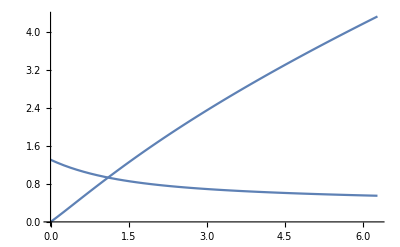

```mathematica
Plot[{r[t], z[t]}/.sol[[1]],{t,0,2 Pi}]
```

```mathematica
S2[{x_,y_,z_}] := 2( x^2 + y^2 - 2 z^2);
S3[{x_,y_,z_}] :=2 z^2(x^2 + y^2) - 1/4(x^2 + y^2)^2 - 2/3 z^4;
```

```mathematica
ϕ[R_, α_, β_] := α S2[R] + β S3[R];
```

```mathematica
H[α_,β_, R_]:= Grad[Grad[ϕ[R,α,β],R],R];
```

```mathematica
Eig[α_,β_, r_] := Eigensystem[H[α,β,{x,y,z}]/.{x->r,y->0,z->0}];
```

```mathematica
H[α,β,{x,y,z}]
```

{{4 α+(-3 x^2-y^2+4 z^2) β,-2 x y β,8 x z β},{-2 x y β,4 α+(-x^2-3 y^2+4 z^2) β,8 y z β},{8 x z β,8 y z β,-8 α+(4 (x^2+y^2)-8 z^2) β}}

```mathematica
Eig[α,β, 1]
```

{{4 α-3 β,-4 (2 α-β),4 α-β},{{1,0,0},{0,0,1},{0,1,0}}}

```mathematica
Eig[1,1, r]
```

{{4-3 r^2,4-r^2,4 (-2+r^2)},{{1,0,0},{0,1,0},{0,0,1}}}

```mathematica
LL =Eig[α,β, r][[1]]
```

{4 α-3 r^2 β,-4 (2 α-r^2 β),4 α-r^2 β}

```mathematica
sol=Solve[LL[[1]] == LL[[2]], r][[2]]
```

{r→(2 √(3/7) √α)/(√β)}

```mathematica
EigS =Eig[α,β, r]/.sol
```

{{-(8 α)/7,-(8 α)/7,(16 α)/7},{{1,0,0},{0,0,1},{0,1,0}}}

```mathematica
asol =Solve[EigS[[1]][[3]] == c, α][[1]]
```

{α→(7 c)/16}

```mathematica
ll =Eig[α,β, r][[1]]
```

{4 α-3 r^2 β,-4 (2 α-r^2 β),4 α-r^2 β}

```mathematica
absol = Solve[{ll[[1]] == ll[[2]],ll[[3]] ==c}, {α,β} ][[1]]
```

{α→(7 c)/16,β→(3 c)/(4 r^2)}

```mathematica
Phisol = (ϕ[{x,y,z},α,β]/.absol)//FullSimplify
```

(c (-3 (x^2+y^2)^2+24 (x^2+y^2) z^2-8 z^4+14 r^2 (x^2+y^2-2 z^2)))/(16 r^2)

```mathematica
H0=(H[α,β, {x,y,z}]/.absol)/.{x ->r Cos[θ], y->r Sin[θ], z->0}//FullSimplify
```

{{1/4 (c-3 c Cos[2 θ]),-3/2 c Cos[θ] Sin[θ],0},{-3/2 c Cos[θ] Sin[θ],1/4 c (1+3 Cos[2 θ]),0},{0,0,-c/2}}

```mathematica
MatrixForm[H0]
```

(1/4 (c-3 c Cos[2 θ]) | -3/2 c Cos[θ] Sin[θ] | 0
-3/2 c Cos[θ] Sin[θ] | 1/4 c (1+3 Cos[2 θ]) | 0
0 | 0 | -c/2)

```mathematica
eis =Eigensystem[H0]//FullSimplify
```

{{c,-c/2,-c/2},{{-Tan[θ],1,0},{0,0,1},{Cot[θ],1,0}}}

```mathematica
MatrixForm[eis]
```

(c | -c/2 | -c/2
{-Tan[θ],1,0} | {0,0,1} | {Cot[θ],1,0})

```mathematica
P[r_, z_, θ_] := r^(2 n)g[θ]f[z^2/r^2];
```

```mathematica
Eq = D[P[r,z, θ],{z,2}] + 1/r D[P[r,z, θ],r] + D[P[r,z,θ],{r,2}] + 1/r^2 D[P[r,z,θ],{θ,2}]==0
```

(2 n r^(-1+2 n) f[z^2/r^2] g[θ]-2 r^(-3+2 n) z^2 g[θ] f'[z^2/r^2])/r+r^(2 n) g[θ] ((2 f'[z^2/r^2])/r^2+(4 z^2 f''[z^2/r^2])/r^4)+g[θ] (2 n (-1+2 n) r^(-2+2 n) f[z^2/r^2]-8 n r^(-4+2 n) z^2 f'[z^2/r^2]+r^(2 n) ((6 z^2 f'[z^2/r^2])/r^4+(4 z^4 f''[z^2/r^2])/r^6))+r^(-2+2 n) f[z^2/r^2] g''[θ]==0

```mathematica
eqs =FullSimplify[Eq/.{r->1, z^2 -> t, z^4-> t^2}]
```

2 g[θ] (2 n^2 f[t]+(1+2 t-4 n t) f'[t]+2 t (1+t) f''[t])+f[t] g''[θ]==0

```mathematica
eqs1=(eqs//.{g[θ]-> Cos[2m θ], g''[θ]-> -4m^2 g[θ]})//FullSimplify
```

Cos[2 m θ] (2 (m-n) (m+n) f[t]+(-1-2 t+4 n t) f'[t]-2 t (1+t) f''[t])==0

```mathematica
FullSimplify[DSolve[eqs1/.θ->0,f[t],t][[1]]/.{C[2]->0,C[1]->1}, { {n,m} ϵ Integers, n >0, m>0}]
```

{f[t]→Hypergeometric2F1[-m-n,m-n,1/2,-t]}

```mathematica
FullSimplify[Hypergeometric2F1[-1,-1,1/2,-t]]
```

1-2 t

```mathematica
FullSimplify[Hypergeometric2F1[-3 ,1,1/2,-t]]
```

1+6 t+8 t^2+(16 t^3)/5

```mathematica
FullSimplify[Hypergeometric2F1[-2,-2,1/2,-t]]
```

1+8/3 (-3+t) t

```mathematica
FunctionExpand[Hypergeometric2F1[-m-n,m-n,1/2,-t],{ m,n ϵ Integers, n >0}]
```

Hypergeometric2F1[-m-n,m-n,1/2,-t]

```mathematica
FullSimplify[Table[Hypergeometric2F1[-m-n,m-n,1/2,-t],{n,0,3},{m,0,2}]]
```

{{1,1+2 t,1+8 t (1+t)},{1-2 t,1,1+6 t+8 t^2+(16 t^3)/5},{1+8/3 (-3+t) t,1-6 t,1},{1-2/5 t (45-60 t+8 t^2),1+16 (-1+t) t,1-10 t}}

```mathematica
F[{x_,y_,z_}, n_, m_] := (x^2 + y^2)^(n-m) (x + I y)^(2 m)Hypergeometric2F1[-m -n,m-n,1/2,-z^2/(x^2+ y^2)]
```

```mathematica
F[{x,y,z}, 1,0]
```

x^2+y^2-2 z^2

```mathematica
F[{x,y,z}, 1,1]
```

(x+ⅈ y)^2

```mathematica
F[{r Cos[θ],r Sin[θ],z}, 1,1]//FullSimplify
```

ⅇ^(2 ⅈ θ) r^2

```mathematica
F[{x,y,z}, 2,1]//FullSimplify
```

(x+ⅈ y)^2 (x^2+y^2-6 z^2)

```mathematica
F[{x,y,z}, 3,3]//FullSimplify
```

(x+ⅈ y)^6

```mathematica
Laplacian[F[{x,y,z}, n, m] ,{x,y,z}]//FullSimplify
```

0

```mathematica
Sub1 = (ⅇ^(ⅈ θ) r)^(2 m)-> r^(2m) Cos[2 m θ];
Sub2 = (ⅇ^(ⅈ θ) r)^(2 m)-> r^(2m) Sin[2 m θ];
```

```mathematica
H =((Grad[Grad[F[{x,y,z}, n,m] ,{x,y,z}],{x,y,z}]/.{x -> r Cos[θ], y->r Sin[θ], z->0})//FullSimplify);
```

```mathematica
h1=FullSimplify[Re[ComplexExpand[H/.Sub1]]/.{Im[X_] :>0, Re[X_] :>X},{r>0, θ >0}]
```

{{2 r^(-2+2 n) (-m^2+n^2+(m^2+(-1+n) n) Cos[2 θ]) Cos[2 m θ],2 (m^2+(-1+n) n) r^(-2+2 n) Cos[2 m θ] Sin[2 θ],0},{2 (m^2+(-1+n) n) r^(-2+2 n) Cos[2 m θ] Sin[2 θ],-2 r^(-2+2 n) (m^2-n^2+(m^2+(-1+n) n) Cos[2 θ]) Cos[2 m θ],0},{0,0,4 (m-n) (m+n) r^(-2+2 n) Cos[2 m θ]}}

```mathematica
MatrixForm[h1]
```

(2 r^(-2+2 n) (-m^2+n^2+(m^2+(-1+n) n) Cos[2 θ]) Cos[2 m θ] | 2 (m^2+(-1+n) n) r^(-2+2 n) Cos[2 m θ] Sin[2 θ] | 0
2 (m^2+(-1+n) n) r^(-2+2 n) Cos[2 m θ] Sin[2 θ] | -2 r^(-2+2 n) (m^2-n^2+(m^2+(-1+n) n) Cos[2 θ]) Cos[2 m θ] | 0
0 | 0 | 4 (m-n) (m+n) r^(-2+2 n) Cos[2 m θ])

```mathematica
h2=FullSimplify[Im[ComplexExpand[H/.Sub2]]/.{Im[X_] :>0, Re[X_] :>X},{r>0, θ >0}]
```

{{2 m (1-2 n) r^(-2+2 n) Sin[2 θ] Sin[2 m θ],2 m (-1+2 n) r^(-2+2 n) Cos[2 θ] Sin[2 m θ],0},{2 m (-1+2 n) r^(-2+2 n) Cos[2 θ] Sin[2 m θ],2 m (-1+2 n) r^(-2+2 n) Sin[2 θ] Sin[2 m θ],0},{0,0,0}}

```mathematica
eig1 =Eigenvalues[h1]//FullSimplify
```

{4 (m-n) (m+n) r^(-2+2 n) Cos[2 m θ],2 n (-1+2 n) r^(-2+2 n) Cos[2 m θ],2 (-2 m^2+n) r^(-2+2 n) Cos[2 m θ]}

```mathematica
MatrixForm[eig1]
```

(4 (m-n) (m+n) r^(-2+2 n) Cos[2 m θ]
2 n (-1+2 n) r^(-2+2 n) Cos[2 m θ]
2 (-2 m^2+n) r^(-2+2 n) Cos[2 m θ])

```mathematica
eig2 =Eigenvalues[h2]//FullSimplify
```

{2 m (1-2 n) r^(-2+2 n) Sin[2 m θ],2 m (-1+2 n) r^(-2+2 n) Sin[2 m θ],0}

```mathematica
MatrixForm[eig2]
```

(2 m (1-2 n) r^(-2+2 n) Sin[2 m θ]
2 m (-1+2 n) r^(-2+2 n) Sin[2 m θ]
0)

```mathematica
MatrixForm[eiv2]
```

((-Sec[2 θ]-Tan[2 θ])/(√(1+(-Sec[2 θ]-Tan[2 θ])^2)) | 1/(√(1+(-Sec[2 θ]-Tan[2 θ])^2)) | 0
(Sec[2 θ]-Tan[2 θ])/(√(1+(Sec[2 θ]-Tan[2 θ])^2)) | 1/(√(1+(Sec[2 θ]-Tan[2 θ])^2)) | 0
0 | 0 | 1)

```mathematica
Plus @@ eig2//FullSimplify
```

0

```mathematica
eiv1=FullSimplify[#/Sqrt[#.#]& /@ Eigenvectors[h1],{Csc[θ] >0, Sec[θ] >0}]
```

{{0,0,1},{Cos[θ],Sin[θ],0},{-Sin[θ],Cos[θ],0}}

```mathematica
MatrixForm[{eig1,eiv1}]
```

(4 (m-n) (m+n) r^(-2+2 n) Cos[2 m θ] | 2 n (-1+2 n) r^(-2+2 n) Cos[2 m θ] | 2 (-2 m^2+n) r^(-2+2 n) Cos[2 m θ]
{0,0,1} | {Cos[θ],Sin[θ],0} | {-Sin[θ],Cos[θ],0})

```mathematica
eiv2 =TrigReduce[#/Sqrt[#.#]& /@ Eigenvectors[h2]]
```

{{(-Sec[2 θ]-Tan[2 θ])/(√(1+(-Sec[2 θ]-Tan[2 θ])^2)),1/(√(1+(-Sec[2 θ]-Tan[2 θ])^2)),0},{(Sec[2 θ]-Tan[2 θ])/(√(1+(Sec[2 θ]-Tan[2 θ])^2)),1/(√(1+(Sec[2 θ]-Tan[2 θ])^2)),0},{0,0,1}}

```mathematica
MatrixForm[eiv2]
```

((-Sec[2 θ]-Tan[2 θ])/(√(1+(-Sec[2 θ]-Tan[2 θ])^2)) | 1/(√(1+(-Sec[2 θ]-Tan[2 θ])^2)) | 0
(Sec[2 θ]-Tan[2 θ])/(√(1+(Sec[2 θ]-Tan[2 θ])^2)) | 1/(√(1+(Sec[2 θ]-Tan[2 θ])^2)) | 0
0 | 0 | 1)

```mathematica
Integrate[Log[a + b Cos[2 θ]],{θ,-Pi,Pi},GenerateConditions->False]
```

ⅈ π^2-π Log[4]+2 π Log[a]+2 π Log[1+√(1-b^2/a^2)]-2 ArcSin[b/a] Log[(a+ⅈ b-a √(1-b^2/a^2))/(a-ⅈ b+a √(1-b^2/a^2))]+2 ArcSin[b/a] Log[(a-ⅈ b-a √(1-b^2/a^2))/(a+ⅈ b+a √(1-b^2/a^2))]+2 ⅈ PolyLog[2,-(ⅈ b)/a-√(1-b^2/a^2)]+2 ⅈ PolyLog[2,(ⅈ b)/a-√(1-b^2/a^2)]-2 ⅈ PolyLog[2,-(ⅈ b)/a+√(1-b^2/a^2)]-2 ⅈ PolyLog[2,(ⅈ b)/a+√(1-b^2/a^2)]

```mathematica
FullSimplify[%221]
```

2 ArcSin[b/a] (-Log[-(ⅈ a (-1+√(1-b^2/a^2)))/b]+Log[(ⅈ a (-1+√(1-b^2/a^2)))/b])+π (ⅈ π-Log[4]+2 Log[a]+2 Log[1+√(1-b^2/a^2)])+2 ⅈ PolyLog[2,-(ⅈ b)/a-√(1-b^2/a^2)]+2 ⅈ PolyLog[2,(ⅈ b)/a-√(1-b^2/a^2)]-2 ⅈ PolyLog[2,-(ⅈ b)/a+√(1-b^2/a^2)]-2 ⅈ PolyLog[2,(ⅈ b)/a+√(1-b^2/a^2)]

```mathematica
LogI =FullSimplify[%222/.{a->1, b->Sin[α]},{-Pi/2<α < Pi/2}]
```

ⅈ (π (π-α+ⅈ Log[4])-2 ⅈ π Log[1+Cos[α]]+2 ⅈ α (Log[ⅈ Tan[α/2]]-Log[Tan[α/2]])+2 PolyLog[2,-ⅇ^(-ⅈ α)]-2 PolyLog[2,ⅇ^(-ⅈ α)]-4 PolyLog[2,ⅇ^(ⅈ α)]+PolyLog[2,ⅇ^(2 ⅈ α)])

```mathematica
RlogI =Simplify[Re[LogI],-Pi<α < Pi]
```

-Im[2 PolyLog[2,-ⅇ^(-ⅈ α)]-2 PolyLog[2,ⅇ^(-ⅈ α)]-4 PolyLog[2,ⅇ^(ⅈ α)]+PolyLog[2,ⅇ^(2 ⅈ α)]]-π Log[4]+2 π Re[Log[1+Cos[α]]]-2 α Re[Log[ⅈ Tan[α/2]]-Log[Tan[α/2]]]

```mathematica
DissInt[a_, α_]=FullSimplify[ Log[a] + RlogI/(2 Pi),{a >0,-Pi< α < Pi}]/.PolyLog[2,z_]:> P[z]
```

-(2 Im[P[-ⅇ^(-ⅈ α)]]-2 Im[P[ⅇ^(-ⅈ α)]]-4 Im[P[ⅇ^(ⅈ α)]]+Im[P[ⅇ^(2 ⅈ α)]])/(2 π)+Log[1/2 a (1+Cos[α])]

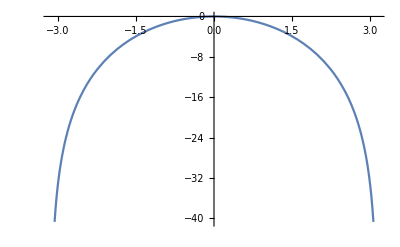

```mathematica
Plot[RlogI,{α,-Pi,Pi}]
```

```mathematica
Integrate[Exp[I q Cos[θ] ]Cos[θ],{θ,-Pi,Pi}, GenerateConditions->False]
```

2 ⅈ π BesselJ[1,q]

```mathematica
Integrate[Exp[I q Cos[θ] ],{θ,-Pi,Pi}, GenerateConditions->False]
```

```mathematica
VZ[z_] =FullSimplify[Integrate[BesselJ[1,q r]BesselJ[0,q r]Exp[- q z]q r ,{q,0,Infinity},GenerateConditions->False], {  r >0, z >0}]
```

(-(z^2 EllipticE[-(4 r^2)/z^2])/(4 r^2+z^2)+EllipticK[-(4 r^2)/z^2])/(π z)

```mathematica
Collect[FullSimplify[Normal[Series[VZ[z],{z,0,2}]],{r >0, z >0}], z]
```

(-2+Log[(64 r^2)/z^2])/(4 π r)

```mathematica
VZInt =NIntegrate[Pi^2(VZ[z]/.r->1)^2 z,{z,0,Infinity},WorkingPrecision->100]
```

0.5

```mathematica
VV[z_] =FullSimplify[Integrate[BesselJ[1,q r]^2Exp[- q z]q r ,{q,0,Infinity},GenerateConditions->False], {  r >0, z >0}]
```

(((2 r^2+z^2) EllipticE[-(4 r^2)/z^2])/(4 r^2+z^2)-EllipticK[-(4 r^2)/z^2])/(π r)

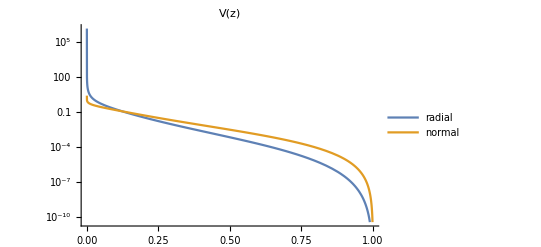

```mathematica
LogPlot[{(VV[z]/.r->1),(VZ[z]/.r->1)}, 
{z,0.,Infinity},PlotLabel->V[z], PlotLegends->{"radial","normal"}]
```

```mathematica
Collect[FullSimplify[Normal[Series[VV[1/x]/.r->1,{x,0,4}]],{ x >0}], x]
```

(3 x^4)/2

```mathematica
Collect[FullSimplify[Normal[Series[VV[z]^2,{z,0,2}]],{r >0, z >0}], z]
```

1/(π^2 z^2)+(5-12 Log[2]-3 Log[(4 r^2)/z^2])/(8 π^2 r^2)

```mathematica
VV2 = FullSimplify[r^2 VV[u r ]^2  u]
```

(u ((2+u^2) EllipticE[-4/u^2]-(4+u^2) EllipticK[-4/u^2])^2)/(π^2 (4+u^2)^2)

```mathematica
Collect[FullSimplify[Normal[Series[VV2,{u,0,2}]],{ u >0}], u]
```

1/(π^2 u)

```mathematica
W[u_] = Pi^2u VV2
```

(u^2 ((2+u^2) EllipticE[-4/u^2]-(4+u^2) EllipticK[-4/u^2])^2)/((4+u^2)^2)

```mathematica
Limit[W[u],u ->Infinity,Direction->"FromBelow"]
```

0

Syntax::sntxi: Incomplete expression; more input is needed .

```mathematica
C0 = -EulerGamma + 3 Log[2]  +2NIntegrate[Log[u] W'[u] - Pi^2(VZ[u]/.r->1)^2 u,{u,0,Infinity},Exclusions->u==0, AccuracyGoal->10, WorkingPrecision->20]
```

1.3433427934186324062